```mathematica
collectLog[expr_]:=Module[{rule1,rule2,a,b,x},rule1=Log[a_]+Log[b_]->Log[a*b];
(expr//.rule1)];
```

```mathematica
Integrate[k^2/(k^2-λ),{k,0,n},PrincipalValue->True,Assumptions->n>0&&0<Re[λ]<n^2&&λ==Re[λ]]
```

n+1/2 √λ Log[-1+(2 n)/(n+√λ)]

```mathematica
μ=0.4
```

0.4

```mathematica
NIntegrate[k^2/(k^2-μ^2)(NIntegrate[ν^2/(k^2-ν^2),{ν,0,k,1},Method->"PrincipalValue"]+k^2(ArcTanh[k]/k+1/(4Pi*k^2))),{k,0,μ,1},Method->"PrincipalValue"]+(μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))*(NIntegrate[ν^2/(μ^2-ν^2),{ν,0,μ,1},Method->"PrincipalValue"]+μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))
```

0.251799

```mathematica
(A[μ]/.{n->1,α->1})^(-2)
```

0.251799+4.49956×10^-17 ⅈ

```mathematica
(μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))^2
```

0.0297333

```mathematica
A[ν]
```

(4 π)/(√(α^2+8 π μ ((-2 n π+α) ArcTanh[μ/n]+4 π μ ArcTanh[μ/n]^2+π (ⅈ π μ (Log[(4 n)/(n-μ)]+Log[n/(n+μ)])+μ Log[n] (-Log[-1+n^2/μ^2]+Log[n-μ]-2 Log[μ]+Log[n+μ])+n Log[(n+μ)/(n-μ)]+μ Log[n+μ] (Log[n-μ]+Log[n+μ]-Log[n^2-μ^2])))+8 π^2 μ^2 (PolyLog[2,(2 n)/(n-μ)]+PolyLog[2,(2 n)/(n+μ)])))

```mathematica
Af[x_]:=A[x]/.{n->1,α->1}
(*Nummerical transform and inverse transform of f(x)=1*)
```

```mathematica
Af[x]
```

(4 π)/(√(1+8 π x ((1-2 π) ArcTanh[x]+4 π x ArcTanh[x]^2+π (ⅈ π x (Log[4/(1-x)]+Log[1/(1+x)])+Log[(1+x)/(1-x)]+x Log[1+x] (Log[1-x]+Log[1+x]-Log[1-x^2])))+8 π^2 x^2 (PolyLog[2,2/(1-x)]+PolyLog[2,2/(1+x)])))

```mathematica
μ=0.2
```

0.2

```mathematica
NIntegrate[Af[μ] k^2/(k^2-μ^2)(NIntegrate[Af[ν] ν^2/(k^2-ν^2),{ν,0,k,1},Method->"PrincipalValue"]+Af[k]k^2(ArcTanh[k]/k+1/(4Pi*k^2))),{k,0,μ,1},Method->"PrincipalValue"]+Af[μ](μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))*(NIntegrate[Af[ν] ν^2/(μ^2-ν^2),{ν,0,μ,1},Method->"PrincipalValue"]+Af[μ]μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))
```

1.-1.25749×10^-17 ⅈ

```mathematica
(*Numerical transform and inverse transform of f(x)=x*)
μ
NIntegrate[Af[μ] k^2/(k^2-μ^2)(NIntegrate[Af[ν] ν^2/(k^2-ν^2)ν,{ν,0,k,1},Method->"PrincipalValue"]+Af[k]k^2k(ArcTanh[k]/k+1/(4Pi*k^2))),{k,0,μ,1},Method->"PrincipalValue"]+Af[μ](μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))*(NIntegrate[Af[ν] ν^2/(μ^2-ν^2)ν,{ν,0,μ,1},Method->"PrincipalValue"]+Af[μ]μ^2μ(ArcTanh[μ]/μ+1/(4Pi*μ^2)))
```

0.2

0.2-1.4399×10^-17 ⅈ

```mathematica
(*Numerical transform and inverse transform of f(x)=x^2*)
μ^2
NIntegrate[Af[μ] k^2/(k^2-μ^2)(NIntegrate[Af[ν] ν^2/(k^2-ν^2)ν^2,{ν,0,k,1},Method->"PrincipalValue"]+Af[k]k^2k^2(ArcTanh[k]/k+1/(4Pi*k^2))),{k,0,μ,1},Method->"PrincipalValue"]+Af[μ](μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))*(NIntegrate[Af[ν] ν^2/(μ^2-ν^2)ν^2,{ν,0,μ,1},Method->"PrincipalValue"]+Af[μ]μ^2μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))
```

0.04

0.04-9.58612×10^-18 ⅈ

```mathematica
(*Numerical transform and inverse transform of f(x)=Sin[x]*)
Sin[μ]
NIntegrate[Af[μ] k^2/(k^2-μ^2)(NIntegrate[Af[ν] ν^2/(k^2-ν^2)Sin[ν],{ν,0,k,1},Method->"PrincipalValue"]+Af[k]k^2Sin[k](ArcTanh[k]/k+1/(4Pi*k^2))),{k,0,μ,1},Method->"PrincipalValue"]+Af[μ](μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))*(NIntegrate[Af[ν] ν^2/(μ^2-ν^2)Sin[ν],{ν,0,μ,1},Method->"PrincipalValue"]+Af[μ]μ^2Sin[μ](ArcTanh[μ]/μ+1/(4Pi*μ^2)))
```

0.198669

0.198669-1.33438×10^-17 ⅈ

```mathematica
(*Numerical inverse transform and transform of f(x)=x^2*)

q=0.2


NIntegrate[Af[ν] ν^2/(q^2-ν^2)(NIntegrate[Af[ν] k^2/(k^2-ν^2),{k,0,ν,1},Method->"PrincipalValue"]+Af[ν]ν^2(ArcTanh[ν]/ν+1/(4Pi*ν^2))),{ν,0,q,1},Method->"PrincipalValue"]+(Af[q]q^2(ArcTanh[q]/q+1/(4Pi*q^2)))*NIntegrate[Af[q] k^2/(k^2-q^2),{k,0,q,1},Method->"PrincipalValue"]+
(Af[q]q^2(ArcTanh[q]/q+1/(4Pi*q^2)))^2
```

0.2

1.+1.31976×10^-16 ⅈ

```mathematica
q=0.2


NIntegrate[Af[ν] ν^2/(q^2-ν^2)(NIntegrate[Af[ν] k^2/(k^2-ν^2)k^3,{k,0,ν,1},Method->"PrincipalValue"]+Af[ν]ν^2ν^3(ArcTanh[ν]/ν+1/(4Pi*ν^2))),{ν,0,q,1},Method->"PrincipalValue"]+(Af[q]q^2(ArcTanh[q]/q+1/(4Pi*q^2)))*NIntegrate[Af[q] k^2/(k^2-q^2)k^3,{k,0,q,1},Method->"PrincipalValue"]+
(Af[q]q^2(ArcTanh[q]/q+1/(4Pi*q^2)))^2q^3
```

0.2

0.008+2.59285×10^-17 ⅈ

```mathematica
NIntegrate[Af[ν] ν^2/(q^2-ν^2)(NIntegrate[Af[ν] k^2/(k^2-ν^2)k^4,{k,0,ν,1},Method->"PrincipalValue"]+Af[ν]ν^2ν^4(ArcTanh[ν]/ν+1/(4Pi*ν^2))),{ν,0,q,1},Method->"PrincipalValue"]+(Af[q]q^2(ArcTanh[q]/q+1/(4Pi*q^2)))*NIntegrate[Af[q] k^2/(k^2-q^2)k^4,{k,0,q,1},Method->"PrincipalValue"]+
(Af[q]q^2(ArcTanh[q]/q+1/(4Pi*q^2)))^2q^4
```

0.0016+2.00536×10^-17 ⅈ

```mathematica
NIntegrate[Af[k]-k^2/(k^2-μ^2)(NIntegrate[Af[k]-ν^2/(k^2-ν^2)ν^2,{ν,0,k,1},Method->"PrincipalValue"]+Af[k]k^2k^2(ArcTanh[k]/k+1/(4Pi*k^2))),{k,0,μ,1},Method->"PrincipalValue"]+Af[μ](μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))*(NIntegrate[Af[μ]-ν^2/(μ^2-ν^2)ν^2,{ν,0,μ,1},Method->"PrincipalValue"]+Af[μ]μ^2μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))
```

0.0400023+3.60903×10^-17 ⅈ

```mathematica
(*Inverse transform and transform of Sin[x]*)
NIntegrate[Af[k]-k^2/(k^2-μ^2)(NIntegrate[Af[k]-ν^2/(k^2-ν^2)Sin[ν],{ν,0,k,1},Method->"PrincipalValue"]+Af[k]k^2Sin[k](ArcTanh[k]/k+1/(4Pi*k^2))),{k,0,μ,1},Method->"PrincipalValue"]+Af[μ](μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))*(NIntegrate[Af[μ]-ν^2/(μ^2-ν^2)Sin[ν],{ν,0,μ,1},Method->"PrincipalValue"]+Af[μ]μ^2Sin[μ](ArcTanh[μ]/μ+1/(4Pi*μ^2)))
```

0.198672+6.37085×10^-17 ⅈ

```mathematica
Sin[μ]
```

0.198669

```mathematica
Af[ν]
```

(4 π)/(√(1+8 π μ ((1-2 π) ArcTanh[μ]+4 π μ ArcTanh[μ]^2+π (ⅈ π μ (Log[4/(1-μ)]+Log[1/(1+μ)])+Log[(1+μ)/(1-μ)]+μ Log[1+μ] (Log[1-μ]+Log[1+μ]-Log[1-μ^2])))+8 π^2 μ^2 (PolyLog[2,2/(1-μ)]+PolyLog[2,2/(1+μ)])))

## Determining the normalization constant

```mathematica
(*Determining the normalization Subscript[A, μ]*)
```

```mathematica
Clear[μ]
```

```mathematica
(*Transform 1/Subscript[A, ν]*)
```

```mathematica
Integrate[1/(k^2-μ^2)μ^2,{μ,0,n},PrincipalValue->True,Assumptions->k>0&&k^2<n^2&&n≥0]+k*ArcTanh[k/n]+α/(4Pi)
```

-n+α/(4 π)+k ArcTanh[k/n]-1/2 k Log[1-(2 k)/(k+n)]

```mathematica
(*-1/2 Log[1-(2 k)/(k+n)]=-1/2  Log[(n-k)/(n+k)]=-1/2  Log[(n-k)/(n+k)]=-1/2Log[1-k/n]+1/2 Log[1+k/n]*)
```

```mathematica
TrigToExp[ArcTanh[k/n]]
```

-1/2 Log[1-k/n]+1/2 Log[1+k/n]

```mathematica
FullSimplify[-n+α/(4 π)+k ArcTanh[k/n]+k ArcTanh[k/n]]
```

-n+α/(4 π)+2 k ArcTanh[k/n]

```mathematica
TrigToExp[-n+α/(4 π)+k (ArcTanh[k/n]+ArcTanh[k/n])]
```

-n+α/(4 π)-k Log[1-k/n]+k Log[1+k/n]

```mathematica
(*Inverse Transform divided by Subscript[A, μ]*)
```

```mathematica
(*First term*)
Clear[t1,t2]
```

```mathematica
t1=Integrate[(-n+α/(4 π)-k Log[1-k/n]+k Log[1+k/n])k^2/(k^2-μ^2),{k,0,n},PrincipalValue->True,Assumptions->μ>0&&μ^2<n^2&&n≥0]
```

1/(4 π)(n α-α μ ArcTanh[μ/n]+2 ⅈ π^2 μ^2 Log[4]+4 ⅈ π^2 μ^2 Log[n]-2 n π μ Log[n-μ]-2 ⅈ π^2 μ^2 Log[n-μ]+2 n π μ Log[n+μ]-2 ⅈ π^2 μ^2 Log[n+μ]+2 π μ^2 PolyLog[2,(2 n)/(n-μ)]+2 π μ^2 PolyLog[2,(2 n)/(n+μ)])

```mathematica
(*Second term*)
```

```mathematica
t2=(μ*ArcTanh[μ/n]+α/(4Pi))*(-n+α/(4 π)+2 μ ArcTanh[μ/n]);
```

```mathematica
(*Total inverse transform*)
```

```mathematica
t1+t2
```

(α/(4 π)+μ ArcTanh[μ/n]) (-n+α/(4 π)+2 μ ArcTanh[μ/n])+1/(4 π)(n α-α μ ArcTanh[μ/n]+2 ⅈ π^2 μ^2 Log[4]+4 ⅈ π^2 μ^2 Log[n]-2 n π μ Log[n-μ]-2 ⅈ π^2 μ^2 Log[n-μ]+2 n π μ Log[n+μ]-2 ⅈ π^2 μ^2 Log[n+μ]+2 π μ^2 PolyLog[2,(2 n)/(n-μ)]+2 π μ^2 PolyLog[2,(2 n)/(n+μ)])

```mathematica
TIT[μ_]:=(α/(4 π)+μ ArcTanh[μ/n]) (-n+α/(4 π)+2 μ ArcTanh[μ/n])+1/(4 π)(n α-α μ ArcTanh[μ/n]+2 ⅈ π^2 μ^2 Log[4]-2 π μ^2 Log[n] Log[-1+n^2/μ^2]+2 ⅈ π^2 μ^2 Log[n/(n-μ)]+2 π μ^2 Log[n] Log[n-μ]-4 π μ^2 Log[n] Log[μ]+2 ⅈ π^2 μ^2 Log[n/(n+μ)]+2 π μ^2 Log[n] Log[n+μ]+2 π μ^2 Log[n-μ] Log[n+μ]+2 π μ^2 Log[n+μ]^2+2 n π μ Log[(n+μ)/(n-μ)]-2 π μ^2 Log[n+μ] Log[n^2-μ^2]+2 π μ^2 PolyLog[2,(2 n)/(n-μ)]+2 π μ^2 PolyLog[2,(2 n)/(n+μ)])
```

```mathematica
TIT[μ]//Simplify
```

1/16 (α^2/π^2-16 n μ ArcTanh[μ/n]+(8 α μ ArcTanh[μ/n])/π+32 μ^2 ArcTanh[μ/n]^2+8 ⅈ π μ^2 Log[4]-8 μ^2 Log[n] Log[-1+n^2/μ^2]+8 ⅈ π μ^2 Log[n/(n-μ)]+8 μ^2 Log[n] Log[n-μ]-16 μ^2 Log[n] Log[μ]+8 ⅈ π μ^2 Log[n/(n+μ)]+8 μ^2 Log[n] Log[n+μ]+8 μ^2 Log[n-μ] Log[n+μ]+8 μ^2 Log[n+μ]^2+8 n μ Log[(n+μ)/(n-μ)]-8 μ^2 Log[n+μ] Log[n^2-μ^2]+8 μ^2 PolyLog[2,(2 n)/(n-μ)]+8 μ^2 PolyLog[2,(2 n)/(n+μ)])

```mathematica
t1+t2//Simplify
```

1/16 (α^2/π^2-16 n μ ArcTanh[μ/n]+(8 α μ ArcTanh[μ/n])/π+32 μ^2 ArcTanh[μ/n]^2+8 ⅈ π μ^2 Log[4]+16 ⅈ π μ^2 Log[n]-8 n μ Log[n-μ]-8 ⅈ π μ^2 Log[n-μ]+8 n μ Log[n+μ]-8 ⅈ π μ^2 Log[n+μ]+8 μ^2 PolyLog[2,(2 n)/(n-μ)]+8 μ^2 PolyLog[2,(2 n)/(n+μ)])

```mathematica
%/.{α->1,μ->2,n->10}
```

1/16 (1/π^2-320 ArcTanh[1/5]+(16 ArcTanh[1/5])/π+128 ArcTanh[1/5]^2+32 ⅈ π Log[4]-160 Log[8]-32 ⅈ π Log[8]+64 ⅈ π Log[10]+160 Log[12]-32 ⅈ π Log[12]+32 PolyLog[2,5/3]+32 PolyLog[2,5/2])

```mathematica
%//N
```

10.1049+7.10543×10^-15 ⅈ

```mathematica
TIT[μ]/.{α->1,μ->2,n->10}
```

(1/(4 π)+2 ArcTanh[1/5]) (-10+1/(4 π)+4 ArcTanh[1/5])+1/(4 π)(10-2 ArcTanh[1/5]-8 ⅈ π^2 Log[6/5]+8 ⅈ π^2 Log[5/4]+40 π Log[3/2]+8 ⅈ π^2 Log[4]-16 π Log[2] Log[10]+8 π Log[8] Log[10]+8 π Log[8] Log[12]+8 π Log[10] Log[12]+8 π Log[12]^2-8 π Log[10] Log[24]-8 π Log[12] Log[96]+8 π PolyLog[2,5/3]+8 π PolyLog[2,5/2])

```mathematica
%//N
```

10.1049-1.13086×10^-15 ⅈ

```mathematica
TIT[μ]//Simplify
```

1/16 (α^2/π^2-16 n μ ArcTanh[μ/n]+(8 α μ ArcTanh[μ/n])/π+32 μ^2 ArcTanh[μ/n]^2+8 ⅈ π μ^2 Log[4]-8 μ^2 Log[n] Log[-1+n^2/μ^2]+8 ⅈ π μ^2 Log[n/(n-μ)]+8 μ^2 Log[n] Log[n-μ]-16 μ^2 Log[n] Log[μ]+8 ⅈ π μ^2 Log[n/(n+μ)]+8 μ^2 Log[n] Log[n+μ]+8 μ^2 Log[n-μ] Log[n+μ]+8 μ^2 Log[n+μ]^2+8 n μ Log[(n+μ)/(n-μ)]-8 μ^2 Log[n+μ] Log[n^2-μ^2]+8 μ^2 PolyLog[2,(2 n)/(n-μ)]+8 μ^2 PolyLog[2,(2 n)/(n+μ)])

```mathematica
%//Expand
```

α^2/(16 π^2)-n μ ArcTanh[μ/n]+(α μ ArcTanh[μ/n])/(2 π)+2 μ^2 ArcTanh[μ/n]^2+1/2 ⅈ π μ^2 Log[4]-1/2 μ^2 Log[n] Log[-1+n^2/μ^2]+1/2 ⅈ π μ^2 Log[n/(n-μ)]+1/2 μ^2 Log[n] Log[n-μ]-μ^2 Log[n] Log[μ]+1/2 ⅈ π μ^2 Log[n/(n+μ)]+1/2 μ^2 Log[n] Log[n+μ]+1/2 μ^2 Log[n-μ] Log[n+μ]+1/2 μ^2 Log[n+μ]^2+1/2 n μ Log[(n+μ)/(n-μ)]-1/2 μ^2 Log[n+μ] Log[n^2-μ^2]+1/2 μ^2 PolyLog[2,(2 n)/(n-μ)]+1/2 μ^2 PolyLog[2,(2 n)/(n+μ)]

```mathematica
%//FullSimplify
```

1/(16 π^2)(α^2+8 π μ ((-2 n π+α) ArcTanh[μ/n]+4 π μ ArcTanh[μ/n]^2+π (ⅈ π μ (Log[(4 n)/(n-μ)]+Log[n/(n+μ)])+μ Log[n] (-Log[-1+n^2/μ^2]+Log[n-μ]-2 Log[μ]+Log[n+μ])+n Log[(n+μ)/(n-μ)]+μ Log[n+μ] (Log[n-μ]+Log[n+μ]-Log[n^2-μ^2])))+8 π^2 μ^2 (PolyLog[2,(2 n)/(n-μ)]+PolyLog[2,(2 n)/(n+μ)]))

```mathematica
InvA[μ_]:=1/(16 π^2)(α^2+8 π μ ((-2 n π+α) ArcTanh[μ/n]+4 π μ ArcTanh[μ/n]^2+π (ⅈ π μ (Log[(4 n)/(n-μ)]+Log[n/(n+μ)])+μ Log[n] (-Log[-1+n^2/μ^2]+Log[n-μ]-2 Log[μ]+Log[n+μ])+n Log[(n+μ)/(n-μ)]+μ Log[n+μ] (Log[n-μ]+Log[n+μ]-Log[n^2-μ^2])))+8 π^2 μ^2 (PolyLog[2,(2 n)/(n-μ)]+PolyLog[2,(2 n)/(n+μ)]))
```

```mathematica
A[μ_]:=(InvA[μ])^(-1/2)
```

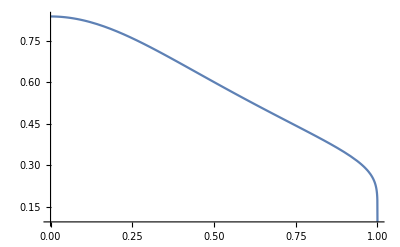

```mathematica
Plot[A[μ]/.{α->15,n->1},{μ,0,1}]
```

```mathematica
A[1]/.α->15
```

(4 π)/(√(225+8 π ((15-2 n π) ArcTanh[1/n]+4 π ArcTanh[1/n]^2+π (ⅈ π (Log[(4 n)/(-1+n)]+Log[n/(1+n)])+n Log[(1+n)/(-1+n)]+Log[n] (Log[-1+n]+Log[1+n]-Log[-1+n^2])+Log[1+n] (Log[-1+n]+Log[1+n]-Log[-1+n^2])))+8 π^2 (PolyLog[2,(2 n)/(-1+n)]+PolyLog[2,(2 n)/(1+n)])))

```mathematica
f[n_]:=(4 π)/(√(225+8 π ((15-2 n π) ArcTanh[1/n]+4 π ArcTanh[1/n]^2+π (ⅈ π (Log[(4 n)/(-1+n)]+Log[n/(1+n)])+n Log[(1+n)/(-1+n)]+Log[n] (Log[-1+n]+Log[1+n]-Log[-1+n^2])+Log[1+n] (Log[-1+n]+Log[1+n]-Log[-1+n^2])))+8 π^2 (PolyLog[2,(2 n)/(-1+n)]+PolyLog[2,(2 n)/(1+n)])))
```

```mathematica
f[1000000000000000000]//N
```

0.588008+0. ⅈ

```mathematica
Clear[μ]
```

```mathematica
A[μ]
```

(4 π)/(√(α^2+8 π μ ((-2 n π+α) ArcTanh[μ/n]+4 π μ ArcTanh[μ/n]^2+π (ⅈ π μ (Log[(4 n)/(n-μ)]+Log[n/(n+μ)])+μ Log[n] (-Log[-1+n^2/μ^2]+Log[n-μ]-2 Log[μ]+Log[n+μ])+n Log[(n+μ)/(n-μ)]+μ Log[n+μ] (Log[n-μ]+Log[n+μ]-Log[n^2-μ^2])))+8 π^2 μ^2 (PolyLog[2,(2 n)/(n-μ)]+PolyLog[2,(2 n)/(n+μ)])))

```mathematica
Expr=%//FullSimplify
```

(4 π)/(√(α^2+8 π μ ((-2 n π+α) ArcTanh[μ/n]+4 π μ ArcTanh[μ/n]^2+π (ⅈ π μ (Log[(4 n)/(n-μ)]+Log[n/(n+μ)])+μ Log[n] (-Log[-1+n^2/μ^2]+Log[n-μ]-2 Log[μ]+Log[n+μ])+n Log[(n+μ)/(n-μ)]+μ Log[n+μ] (Log[n-μ]+Log[n+μ]-Log[n^2-μ^2])))+8 π^2 μ^2 (PolyLog[2,(2 n)/(n-μ)]+PolyLog[2,(2 n)/(n+μ)])))

```mathematica
Expr2=Expr//collectLog
```

(4 π)/(√(α^2+8 π μ ((-2 n π+α) ArcTanh[μ/n]+4 π μ ArcTanh[μ/n]^2+π (ⅈ π μ Log[(4 n^2)/((n-μ) (n+μ))]+n Log[(n+μ)/(n-μ)]+μ Log[n] (-Log[-1+n^2/μ^2]-2 Log[μ]+Log[(n-μ) (n+μ)])+μ Log[n+μ] (Log[(n-μ) (n+μ)]-Log[n^2-μ^2])))+8 π^2 μ^2 (PolyLog[2,(2 n)/(n-μ)]+PolyLog[2,(2 n)/(n+μ)])))

```mathematica
%/.{-2 Log[μ]->-Log[μ^2]}
```

(4 π)/(√(α^2+8 π μ ((-2 n π+α) ArcTanh[μ/n]+4 π μ ArcTanh[μ/n]^2+π (ⅈ π μ Log[(4 n^2)/((n-μ) (n+μ))]+n Log[(n+μ)/(n-μ)]+μ Log[n] (-Log[-1+n^2/μ^2]-Log[μ^2]+Log[(n-μ) (n+μ)])+μ Log[n+μ] (Log[(n-μ) (n+μ)]-Log[n^2-μ^2])))+8 π^2 μ^2 (PolyLog[2,(2 n)/(n-μ)]+PolyLog[2,(2 n)/(n+μ)])))

```mathematica
Expr3=Expr2//.{-2 Log[μ]->-Log[μ^2],-Log[a_]->Log[1/a]}//collectLog
```

(4 π)/(√(α^2+8 π μ ((-2 n π+α) ArcTanh[μ/n]+4 π μ ArcTanh[μ/n]^2+π (ⅈ π μ Log[(4 n^2)/((n-μ) (n+μ))]+n Log[(n+μ)/(n-μ)]+μ Log[n] Log[((n-μ) (n+μ))/((-1+n^2/μ^2) μ^2)]+μ Log[n+μ] Log[((n-μ) (n+μ))/(n^2-μ^2)]))+8 π^2 μ^2 (PolyLog[2,(2 n)/(n-μ)]+PolyLog[2,(2 n)/(n+μ)])))

```mathematica
%//Simplify
```

(4 π)/(√(α^2-16 n π^2 μ ArcTanh[μ/n]+8 π α μ ArcTanh[μ/n]+32 π^2 μ^2 ArcTanh[μ/n]^2+8 n π^2 μ Log[(n+μ)/(n-μ)]+8 ⅈ π^3 μ^2 Log[(4 n^2)/(n^2-μ^2)]+8 π^2 μ^2 PolyLog[2,(2 n)/(n-μ)]+8 π^2 μ^2 PolyLog[2,(2 n)/(n+μ)]))

```mathematica
%//TraditionalForm
```

(4 π)/(√(α^2+8 ⅈ π^3 μ^2 log((4 n^2)/(n^2-μ^2))+8 π α μ tanh^-1(μ/n)+32 π^2 μ^2 (tanh^-1(μ/n))^2+8 π^2 μ n log((μ+n)/(n-μ))-16 π^2 μ n tanh^-1(μ/n)+8 π^2 μ^2 2(2 n)/(n-μ)+8 π^2 μ^2 2(2 n)/(n+μ)))

```mathematica
%//TeXForm
```

\frac{4 \pi }{\sqrt{\alpha ^2+8 i \pi ^3 \mu ^2 \log \left(\frac{4 n^2}{n^2-\mu
   ^2}\right)+8 \pi  \alpha  \mu  \tanh ^{-1}\left(\frac{\mu }{n}\right)+32 \pi
   ^2 \mu ^2 \tanh ^{-1}\left(\frac{\mu }{n}\right)^2+8 \pi ^2 \mu  n \log
   \left(\frac{\mu +n}{n-\mu }\right)-16 \pi ^2 \mu  n \tanh ^{-1}\left(\frac{\mu
   }{n}\right)+8 \pi ^2 \mu ^2 \text{Li}_2\left(\frac{2 n}{n-\mu }\right)+8 \pi
   ^2 \mu ^2 \text{Li}_2\left(\frac{2 n}{n+\mu }\right)}}

```mathematica
Integrate[(1/(k^2+λ))k^2,{k,0,n}]
```

ConditionalExpression[n-√λ ArcTan[n/(√λ)],Re[(√λ)/n]≠0||Im[(√λ)/n]>1||Im[(√λ)/n]<-1]

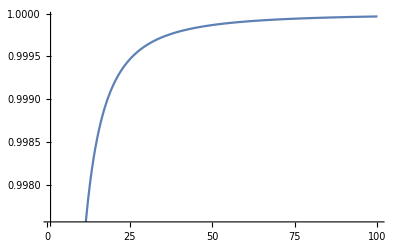

```mathematica
Plot[x ArcTan[1/x],{x,1,100}]
```

```mathematica
Eigenvectors[{{a-b,a},{a,2a-b}}]
```

{{1/2 (-1-√5),1},{1/2 (-1+√5),1}}

```mathematica
Eigenvalues[{{a-b,a},{a,2a-b}}]
```

{1/2 (3 a-√5 a-2 b),1/2 (3 a+√5 a-2 b)}

## Overlap of ground-state for different couplings

```mathematica
Integrate[k^2/(k^2-λ)1/(k^2-λ),{k,0,n},Assumptions->n>0&&Re[λ]<0&&λ==Re[λ]]
```

1/2 (n/(-n^2+λ)-ArcTanh[n/(√λ)]/(√λ))

```mathematica
(*normalization*)
```

```mathematica
Α[λ_]:=1/Sqrt[1/2 (n/(-n^2+λ)-ArcTanh[n/(√λ)]/(√λ))]
```

```mathematica
(*Overlap*)
Α[λ]Α[μ]Integrate[k^2/(k^2-λ)1/(k^2-μ),{k,0,n},Assumptions->n>0&&Re[λ]<0&&λ==Re[λ]&&Re[μ]<0&&μ==Re[μ]]
```

(2 (-√λ ArcTanh[n/(√λ)]+√μ ArcTanh[n/(√μ)]))/((λ-μ) √(n/(-n^2+λ)-ArcTanh[n/(√λ)]/(√λ)) √(n/(-n^2+μ)-ArcTanh[n/(√μ)]/(√μ)))

```mathematica
%^2//FullSimplify
```

(4 (√λ ArcTanh[n/(√λ)]-√μ ArcTanh[n/(√μ)])^2)/((λ-μ)^2 (n/(-n^2+λ)-ArcTanh[n/(√λ)]/(√λ)) (n/(-n^2+μ)-ArcTanh[n/(√μ)]/(√μ)))

```mathematica
%//Expand
```

(4 λ ArcTanh[n/(√λ)]^2)/((λ-μ)^2 (n/(-n^2+λ)-ArcTanh[n/(√λ)]/(√λ)) (n/(-n^2+μ)-ArcTanh[n/(√μ)]/(√μ)))-(8 √λ √μ ArcTanh[n/(√λ)] ArcTanh[n/(√μ)])/((λ-μ)^2 (n/(-n^2+λ)-ArcTanh[n/(√λ)]/(√λ)) (n/(-n^2+μ)-ArcTanh[n/(√μ)]/(√μ)))+(4 μ ArcTanh[n/(√μ)]^2)/((λ-μ)^2 (n/(-n^2+λ)-ArcTanh[n/(√λ)]/(√λ)) (n/(-n^2+μ)-ArcTanh[n/(√μ)]/(√μ)))

```mathematica
%//FullSimplify
```

(4 (n^2-λ) √λ (n^2-μ) √μ (√λ ArcTanh[n/(√λ)]-√μ ArcTanh[n/(√μ)])^2)/((λ-μ)^2 (n √λ+(n^2-λ) ArcTanh[n/(√λ)]) (n √μ+(n^2-μ) ArcTanh[n/(√μ)]))

```mathematica
1-%//FullSimplify
```

1+(4 √λ (-n^2+λ) (n^2-μ) √μ (√λ ArcTanh[n/(√λ)]-√μ ArcTanh[n/(√μ)])^2)/((λ-μ)^2 (n √λ+(n^2-λ) ArcTanh[n/(√λ)]) (n √μ+(n^2-μ) ArcTanh[n/(√μ)]))

```mathematica
TrigToExp[1+(4 √λ (-n^2+λ) (n^2-μ) √μ (√λ ArcTanh[n/(√λ)]-√μ ArcTanh[n/(√μ)])^2)/((λ-μ)^2 (n √λ+(n^2-λ) ArcTanh[n/(√λ)]) (n √μ+(n^2-μ) ArcTanh[n/(√μ)]))]
```

1+(4 √λ (-n^2+λ) (n^2-μ) √μ (1/2 √λ (-Log[1-n/(√λ)]+Log[1+n/(√λ)])-1/2 √μ (-Log[1-n/(√μ)]+Log[1+n/(√μ)]))^2)/((λ-μ)^2 (n √λ+1/2 (n^2-λ) (-Log[1-n/(√λ)]+Log[1+n/(√λ)])) (n √μ+1/2 (n^2-μ) (-Log[1-n/(√μ)]+Log[1+n/(√μ)])))

```mathematica
%//FullSimplify
```

1+(√λ (-n^2+λ) (n^2-μ) √μ (2 √λ ArcTanh[n/(√λ)]-2 √μ ArcTanh[n/(√μ)])^2)/((λ-μ)^2 (n √λ+(n^2-λ) ArcTanh[n/(√λ)]) (n √μ+(n^2-μ) ArcTanh[n/(√μ)]))

```mathematica
Limit[%,n->Infinity]
```

1+(4 (λ+μ+2 √(-1/λ) λ √(-1/μ) μ))/(√(-1/λ) (λ-μ)^2 √(-1/μ))

```mathematica
Limit[%,λ->μ]
```

1

```mathematica
Limit[(-√λ ArcTanh[n/(√λ)]+√μ ArcTanh[n/(√μ)])/(λ-μ),n->Infinity]
```

(π (√(-1/λ) λ+1/(√(-1/μ))))/(2 (λ-μ))

```mathematica
Limit[ArcTanh[s],s->Infinity]
```

-(ⅈ π)/2

```mathematica
Limit[A[μ]A[λ],n->Infinity]
```

0

```mathematica
Limit[A[μ],n->Infinity]
```

0

```mathematica
Limit[(-√λ ArcTanh[n/(√λ)]+√μ ArcTanh[n/(√μ)])/(λ-μ),μ->λ]
```

(n √λ+(n^2-λ) ArcTanh[n/(√λ)])/(2 √λ (-n^2+λ))

```mathematica
ArcTan[Sqrt[3]]
```

π/3

```mathematica
Tan[Pi/4]
```

1

```mathematica
ArcTan[1/Sqrt[3]]
```

π/6

```mathematica
Tan[Pi/Sqrt[6]]
```

Tan[π/(√6)]

```mathematica
//N
```

```mathematica
%//N
```

0.927295

```mathematica
Integrate[1/(x^2+λ)x^2,{x,0,n},Assumptions->λ>0&&λ==Re[λ]]
```

ConditionalExpression[n-√λ ArcTan[n/(√λ)], Re[n]≥0&&Im[n]==0]